```mathematica
(-1)^Range[100]
```

{-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1,-1,1}

```mathematica
Round[Fourier[%147],.01]//Length
```

100

```mathematica
%154
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-10.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Fourier[%154~Join~ConstantArray[0.,400]~Join~%154];
Max[Abs[Im[%]]]
Re[%%];
```

2.17558×10^-16

```mathematica
Length[%191]
```

600

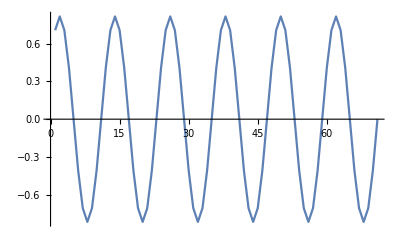

```mathematica
ListLinePlot[%191[[30;;100]]]
```

```mathematica
l=step/@Range[200000];
```

```mathematica
ListPlot[l]
```

-Graphics-

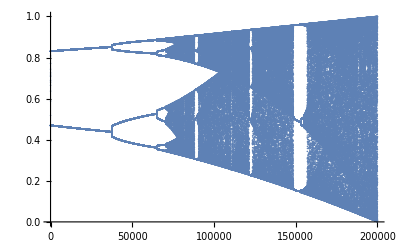

```mathematica
ListPlot[Abs[Reverse@Fourier[Fourier[l]]]]
```

```mathematica
nl=12;
in=l[[10^5;;10^5+nl]];
Fourier[in];
%[[;;nl/2]]~Join~ConstantArray[0.,nl*9]~Join~%[[nl/2+1;;]];
rff=Reverse@Abs[Fourier[%]];
```

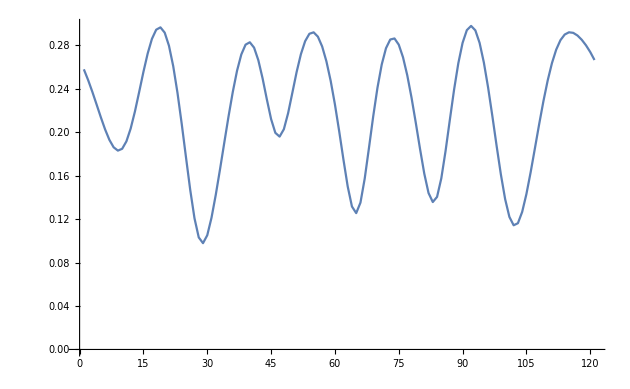

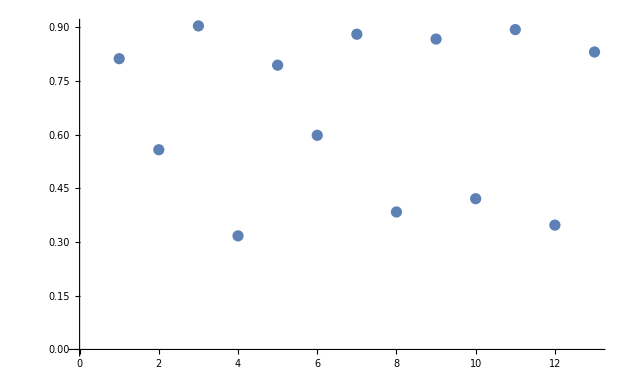

```mathematica
ListLinePlot[rff]
ListPlot[in]
```

```mathematica
Wavelet
```

```mathematica
Clear[step]
r1=10/3;
r2=4;
f=440;
t=300;
step[0]=Random[]
step[i_]:=step[i]=(r1+i(r2-r1)/(2f t)) step[i-1](1-step[i-1])
```

0.401843

```mathematica
l=step/@Range[2f t];
```

```mathematica
i=Interpolation[l,InterpolationOrder->12];
```

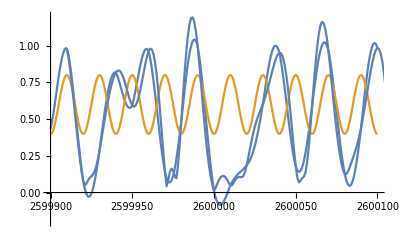

```mathematica
a=2.6*10^6-100;
b=2.6*10^6+100;
Show[
{Plot[{i[x/10],(1-Cos[Pi x/10])/5+.4},{x,a,b},PlotRange->{-.2,1.2}],
ListLinePlot[Transpose[{Range[a+10,b+10],Sqrt[10]rff[[a;;b]]}]]}]
```

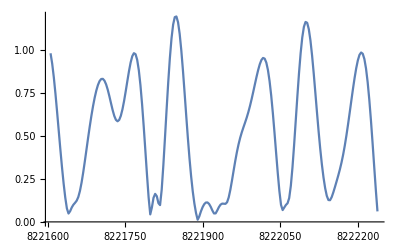

```mathematica
ListLinePlot[Transpose[{Range[a,b],rff[[a;;b]]}]]
```

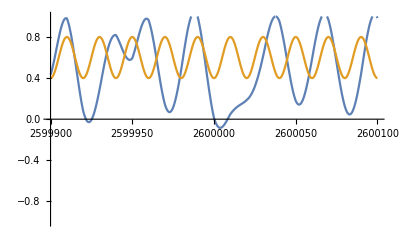

```mathematica
Plot[{i[x/10],(1-Cos[Pi x/10])/5+.4},{x,a,b},PlotRange->{-1,1}]
```

```mathematica
nl=Length@l;
in=l;
Fourier[in];
%[[;;nl/2]]~Join~ConstantArray[0.,nl*9]~Join~%[[nl/2+1;;]];
rff=Reverse@Abs[Fourier[%]];
```

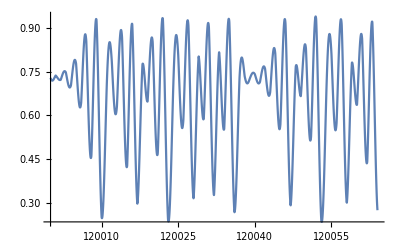

```mathematica
Plot[i[x],{x,1.2*10^5,1.2*10^5+64},PlotRange->All]
```

```mathematica
?Play
```

Play[f,{t,t_min,t_max}] creates an object that plays as a sound whose amplitude is given by f as a function of time t in seconds between t_min and t_max.

```mathematica
Export["/home/adam/smoov.wav",Play[i[1+800t],{t,0,250-1/800}]]
```

/home/adam/smoov.wav

```mathematica
200000/800
```

250